# Plane Curve

### Author

Eric W. Weisstein
December 30, 2010

This notebook downloaded from http://mathworld.wolfram.com/notebooks/PlaneCurves/PlaneCurve.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/PlaneCurve.html.

©2010 Wolfram Research, Inc. except for portions noted otherwise

## Graphic

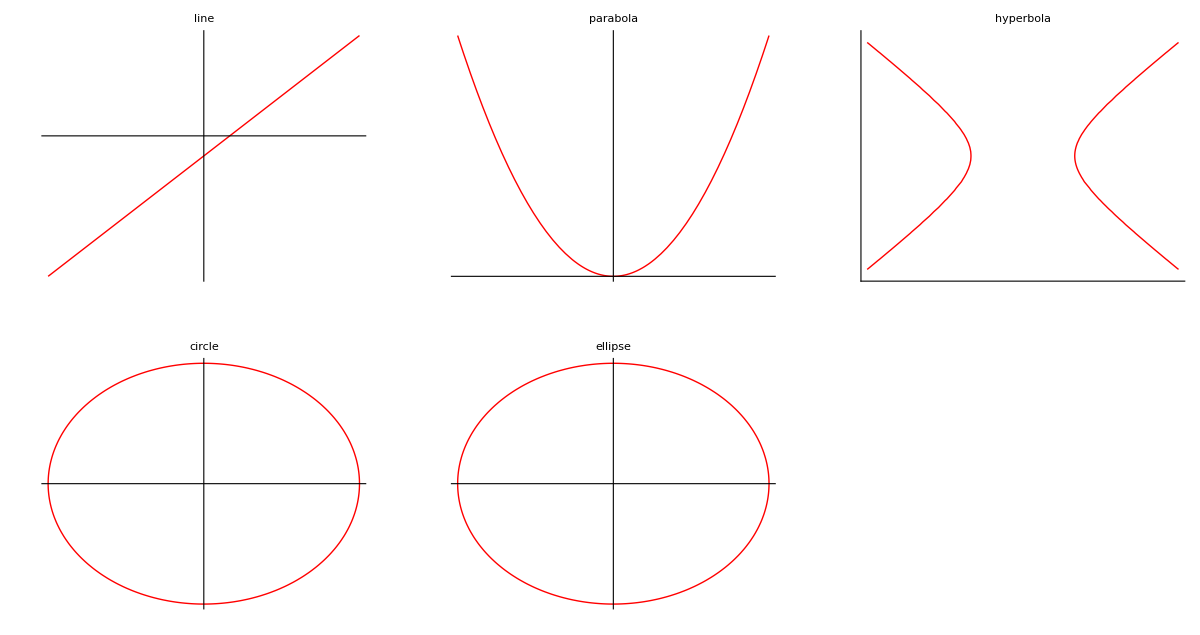

```mathematica
GraphicsGrid[{
{
Plot[3(x-1)+2,{x,-2,2},PlotLabel->"line",BaseStyle->Italic,Ticks->None,PlotStyle->Red],
Plot[x^2,{x,-2,2},PlotLabel->"parabola",BaseStyle->Italic,Ticks->None,PlotStyle->Red],
ContourPlot[x^2/1^2-y^2/1^2-1,{x,-3,3},{y,-3,3},AspectRatio->Automatic,Contours->{0},ContourShading->None,PlotLabel->"hyperbola",BaseStyle->Italic,Ticks->None,ContourStyle->Red,Frame->False,Axes->True,Ticks->False]
},
{
ParametricPlot[{Cos[t],Sin[t]},{t,0,2π},PlotStyle->Red,Ticks->None,PlotLabel->"circle",BaseStyle->Italic],
ParametricPlot[{Cos[t],.8Sin[t]},{t,0,2π},PlotStyle->Red,Ticks->None,PlotLabel->"ellipse",BaseStyle->Italic]
}}]
```